## Define payoffs and fitness

```mathematica
(*s1 and s2 are individuals, each represented by a vector (x,y) *)
Payoff[{s1_,s2_}]:=Module[{bx,by,cx,cy},
bx=(s1⟦1⟧+s2⟦1⟧)-b(s1⟦1⟧+s2⟦1⟧)^2;
by=(s1⟦2⟧+s2⟦2⟧)-b(s1⟦2⟧+s2⟦2⟧)^2;
cx=c (s1⟦1⟧-d (s1⟦1⟧)^2);
cy=c (s1⟦2⟧-d (s1⟦2⟧)^2);
(1-α) (bx-cx)+α (by-cy)]
```

```mathematica
P[s_]:=ArrayReshape[Payoff/@Tuples[s,2],{Length[s],Length[s]}]
```

```mathematica
Frequencies[s_]:=Module[{f},f=Inverse[P[s]] . ConstantArray[1,Length[s]];f/Total[f]]
```

```mathematica
InvasionFitness[{invader_, population_},frequencies_]:=Module[{f,mutantPayoffs,g,residentPayoffs,mutantFitness,residentFitness},
(*Calculate payoffs of mutant*)
f[r_]:=Payoff[{invader,population⟦r⟧}];
mutantPayoffs=f/@ Range[Length[population]];

(*Calculate payoffs of resident*)
g[r_]:=Payoff[{population⟦1⟧,population⟦r⟧}];
residentPayoffs=g/@Range[Length[population]];

mutantFitness=Total[mutantPayoffs*frequencies];
residentFitness=Total[residentPayoffs*frequencies];

(mutantFitness-residentFitness)(*Mutant invasion fitness at n-hat*)
]
```

## Numerical simulation

```mathematica
b=1.05;c=0.9;d=1.65;ess=-(c-1)/(2 (2 b-c d));max=1/(4 b); α=0.5;
```

```mathematica
(*Rows: strain number; Columns: trait x, y*)
s={{s1x[τ],s1y[τ]},{s2x[τ],s2y[τ]}}; s//MatrixForm
```

(s1x[τ] | s1y[τ]
s2x[τ] | s2y[τ])

Numerical simulations show that the strains diverge toward (0, max) and (max, 0) or toward (0, 0) and (max, max), depending on starting condition:

```mathematica
IF=InvasionFitness[{{mx,my},s},Frequencies[s]];
SG1x=D[IF,mx]/.{mx->s1x[τ],my->s1y[τ]};
SG2x=D[IF,mx]/.{mx->s2x[τ],my->s2y[τ]};
SG1y=D[IF,my]/.{mx->s1x[τ],my->s1y[τ]};
SG2y=D[IF,my]/.{mx->s2x[τ],my->s2y[τ]};
```

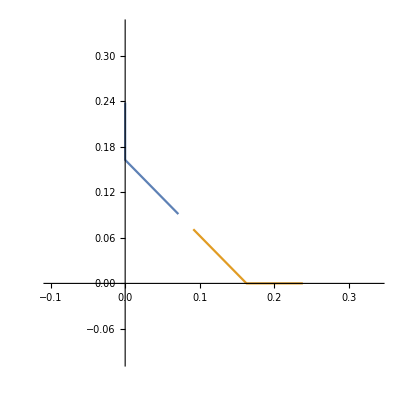

```mathematica
sol=NDSolve[{
D[s⟦1,1⟧,τ]==Piecewise[{{Frequencies[s]⟦1⟧*SG1x, 0<s⟦1,1⟧<max}, {0, True}}],

D[s⟦1,2⟧,τ]==Piecewise[{{Frequencies[s]⟦1⟧*SG1y, 0<s⟦1,2⟧<max}, {0, True}}],
D[s⟦2,1⟧,τ]==Piecewise[{{Frequencies[s]⟦2⟧*SG2x, 0<s⟦2,1⟧<max}, {0, True}}],
D[s⟦2,2⟧,τ]==Piecewise[{{Frequencies[s]⟦2⟧*SG2y, 0<s⟦2,2⟧<max}, {0, True}}],
(s⟦1,1⟧/.τ->0)==(ess-0.01),
(s⟦1,2⟧/.τ->0)==(ess+0.01),
(s⟦2,1⟧/.τ->0)==(ess+0.01),
(s⟦2,2⟧/.τ->0)==(ess-0.01)
},
{s⟦1,1⟧,s⟦1,2⟧,s⟦2,1⟧,s⟦2,2⟧},
{τ,0,50}
];
ParametricPlot[{Evaluate[{s1x[τ],s1y[τ]}/.sol],Evaluate[{s2x[τ],s2y[τ]}/.sol]},{τ,0,50},PlotRange->{{-0.1,max+0.1},{-0.1,max+0.1}}]
```

## Invasion of a third strain, starting from (0,0) and (max, max)

```mathematica
Clear[max,α]
```

```mathematica
(*Rows: strain number; Columns: trait x, y*)
s={{0,0},{max,max}}; s//MatrixForm
```

(0 | 0
max | max)

```mathematica
Payoff[{s1_,s2_}]:=(1-α)(Be[s1⟦1⟧+s2⟦1⟧]-Co[s1⟦1⟧])+α(Be[s1⟦2⟧+s2⟦2⟧]-Co[s1⟦2⟧])
P[s]//FullSimplify;
%/.{Be[0]->0, Co[0]->0}/.α->0.5//FullSimplify//MatrixForm
```

(0 | Be[max]
Be[max]-Co[max] | Be[2 max]-Co[max])

```mathematica
freqs=Frequencies[s]/.{Be[0]->0, Co[0]->0}//FullSimplify
```

{(Be[max]-Be[2 max]+Co[max])/(2 Be[max]-Be[2 max]),(Be[max]-Co[max])/(2 Be[max]-Be[2 max])}

```mathematica
(*Calculate payoffs of mutant*)
f[r_]:=Payoff[{{mx,my},s⟦r⟧}]
f/@ Range[Length[s]]
mutpay=Total[%*freqs]/.{mx->0,my->max}/.{α->0.5,Be[0]->0, Co[0]->0}//FullSimplify
```

{(1-α) (Be[mx]-Co[mx])+α (Be[my]-Co[my]),(1-α) (Be[max+mx]-Co[mx])+α (Be[max+my]-Co[my])}

0.+(1. Be[max]^2)/(2 Be[max]-Be[2 max])-(1. Be[max] Co[max])/(2 Be[max]-Be[2 max])

```mathematica
(*Calculate payoffs of resident*)
f[r_]:=Payoff[{{0,0},s⟦r⟧}]
f/@ Range[Length[s]]
respay=Total[%*freqs]/.{α->0.5,Be[0]->0, Co[0]->0}//FullSimplify
```

{(1-α) (Be[0]-Co[0])+α (Be[0]-Co[0]),(1-α) (Be[max]-Co[0])+α (Be[max]-Co[0])}

0.+(1. Be[max] (Be[max]-Co[max]))/(2 Be[max]-Be[2 max])

```mathematica
mutpay-respay//FullSimplify
```

0.

## Invasion of a third strain, starting from (0, max) and (max, 0)

```mathematica
Clear[max,α]
```

```mathematica
(*Rows: strain number; Columns: trait x, y*)
s={{max,0},{0,max}}; s//MatrixForm
```

(max | 0
0 | max)

```mathematica
Payoff[{s1_,s2_}]:=(1-α)(Be[s1⟦1⟧+s2⟦1⟧]-Co[s1⟦1⟧])+α(Be[s1⟦2⟧+s2⟦2⟧]-Co[s1⟦2⟧])
P[s]//FullSimplify;
%/.{Be[0]->0, Co[0]->0}//FullSimplify//MatrixForm
```

(-(-1+α) (Be[2 max]-Co[max]) | Be[max]+(-1+α) Co[max]
Be[max]-α Co[max] | α (Be[2 max]-Co[max]))

```mathematica
freqs=Frequencies[s]/.{Be[0]->0, Co[0]->0}/.{α->0.5}//FullSimplify
```

{0.5,0.5}

```mathematica
(*Calculate payoffs of mutant*)
f[r_]:=Payoff[{{mx,my},s⟦r⟧}]
tmp=f/@ Range[Length[s]]
mutdef=Total[tmp*freqs]/.{mx->0,my->0}/.{α->0.5,Be[0]->0, Co[0]->0}//FullSimplify
mutcoop=Total[tmp*freqs]/.{mx->max,my->max}/.{α->0.5,Be[0]->0, Co[0]->0}//FullSimplify
```

{(1-α) (Be[max+mx]-Co[mx])+α (Be[my]-Co[my]),(1-α) (Be[mx]-Co[mx])+α (Be[max+my]-Co[my])}

0.+0.5 Be[max]

0.5 Be[max]+0.5 Be[2 max]-1. Co[max]

```mathematica
(*Calculate payoffs of resident*)
f[r_]:=Payoff[{{0,max},s⟦r⟧}]
f/@ Range[Length[s]]
respay=Total[%*freqs]/.{α->0.5,Be[0]->0, Co[0]->0}//FullSimplify
```

{(1-α) (Be[max]-Co[0])+α (Be[max]-Co[max]),(1-α) (Be[0]-Co[0])+α (Be[2 max]-Co[max])}

0.+0.5 Be[max]+0.25 Be[2 max]-0.5 Co[max]

## Invasion of a fourth strain, starting from specialists + defector

```mathematica
Clear[max,α]
```

```mathematica
(*Rows: strain number; Columns: trait x, y*)
s={{max,0},{0,max},{0,0}}; s//MatrixForm
```

(max | 0
0 | max
0 | 0)

```mathematica
Payoff[{s1_,s2_}]:=(1-α)(Be[s1⟦1⟧+s2⟦1⟧]-Co[s1⟦1⟧])+α(Be[s1⟦2⟧+s2⟦2⟧]-Co[s1⟦2⟧])
P[s]//FullSimplify;
%/.{Be[0]->0, Co[0]->0}//FullSimplify//MatrixForm
```

(-(-1+α) (Be[2 max]-Co[max]) | Be[max]+(-1+α) Co[max] | -(-1+α) (Be[max]-Co[max])
Be[max]-α Co[max] | α (Be[2 max]-Co[max]) | α (Be[max]-Co[max])
-(-1+α) Be[max] | α Be[max] | 0)

```mathematica
freqs=Frequencies[s]/.{Be[0]->0, Co[0]->0}/.{α->0.5}//FullSimplify;
```

```mathematica
(*Calculate payoffs of mutant*)
f[r_]:=Payoff[{{max,max},s⟦r⟧}]
tmp=f/@ Range[Length[s]];
cooppay=Total[tmp*freqs]/.{mx->max,my->max}/.{α->0.5,Be[0]->0, Co[0]->0}//FullSimplify;
```

```mathematica
(*Calculate payoffs of resident*)
f[r_]:=Payoff[{{max,max},s⟦r⟧}]
f/@ Range[Length[s]];
respay=Total[%*freqs]/.{α->0.5,Be[0]->0, Co[0]->0}//FullSimplify;
```

```mathematica
cooppay-respay/.{α->0.5,Be[0]->0, Co[0]->0}//FullSimplify
```

0.

## Invasion of a fourth strain, starting from specialists + cooperator

```mathematica
Clear[max,α]
```

```mathematica
(*Rows: strain number; Columns: trait x, y*)
s={{max,0},{0,max},{max,max}}; s//MatrixForm
```

(max | 0
0 | max
max | max)

```mathematica
Payoff[{s1_,s2_}]:=(1-α)(Be[s1⟦1⟧+s2⟦1⟧]-Co[s1⟦1⟧])+α(Be[s1⟦2⟧+s2⟦2⟧]-Co[s1⟦2⟧])
P[s]//FullSimplify;
%/.{Be[0]->0, Co[0]->0}//FullSimplify//MatrixForm
```

(-(-1+α) (Be[2 max]-Co[max]) | Be[max]+(-1+α) Co[max] | α Be[max]-(-1+α) (Be[2 max]-Co[max])
Be[max]-α Co[max] | α (Be[2 max]-Co[max]) | Be[max]-α Be[max]+α Be[2 max]-α Co[max]
α Be[max]-(-1+α) Be[2 max]-Co[max] | Be[max]-α Be[max]+α Be[2 max]-Co[max] | Be[2 max]-Co[max])

```mathematica
freqs=Frequencies[s]/.{Be[0]->0, Co[0]->0}/.{α->0.5}//FullSimplify;
```

```mathematica
(*Calculate payoffs of mutant*)
f[r_]:=Payoff[{{0,0},s⟦r⟧}]
tmp=f/@ Range[Length[s]];
cooppay=Total[tmp*freqs]/.{α->0.5,Be[0]->0, Co[0]->0}//FullSimplify;
```

```mathematica
(*Calculate payoffs of resident*)
f[r_]:=Payoff[{{0,0},s⟦r⟧}]
f/@ Range[Length[s]];
respay=Total[%*freqs]/.{α->0.5,Be[0]->0, Co[0]->0}//FullSimplify;
```

```mathematica
cooppay-respay/.{α->0.5,Be[0]->0, Co[0]->0}//FullSimplify
```

0.